```mathematica
<<UtilityManager`
```

```mathematica
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

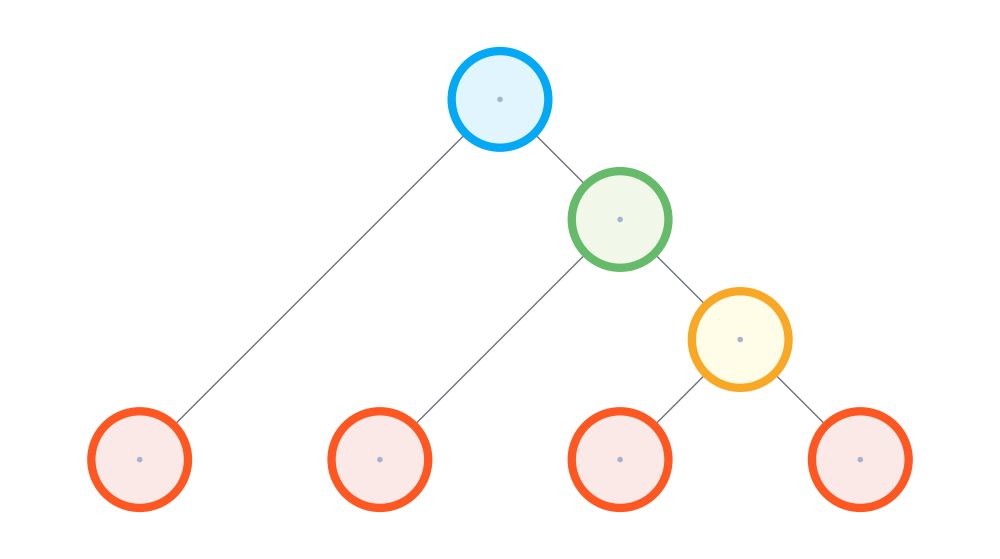

```mathematica
δ=Ramp[{
{0,2,4,6},
{0,0,8,10},
{0,0,0,12},
{0,0,0,0}
}];
δ=δ+Transpose[δ];
{d,δm}=FichetUltrametric[δ];
extree=BinaryTreeFromUltrametric[δm];
{A,B}=PhyloTreeCone[δ,d];
special=FindSpecialVertex[δm,A,B];
weight=PropertyValue[{extree,special},VertexLabels];
gextree=PrettyTreeForm[extree,
ImageSize->1000,FontSize->50,VertexSize->0.12,
VertexColors->{special->blueScheme,{1,3}->whiteScheme,2->redScheme,{4,5}->orangeScheme,{1,2,3,4}->redScheme}
]
savePNG[gextree]
```

```mathematica
ext=ComputeExtreme[A,B];
ultrametrics=UltrametricFromVector/@ext[[All,2;;]];
extrees=BinaryTreeFromUltrametric/@ultrametrics;
specials=Flatten[Position[#,weight]]&/@((Values@KeySort@PropertyValue[#,VertexLabels])&/@extrees);
gextrees=MapThread[PrettyTreeForm[#1,ImageSize->150,FontSize->8,VertexSize->0.12,
VertexColors->{#2->purpleScheme,{1,3}->whiteScheme,2->redScheme,{4,5}->orangeScheme,Cases[{6,7,8,9},Except@@#2]->whiteScheme}
]&,{extrees,specials}]
Table[Export[NotebookDirectory[]<>"prop1-2-ext"<>ToString[i]<>".pdf",gextrees[[i]]],{i,1,Length[gextrees]}];
```

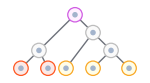

```mathematica
δ=Ramp[{
{0,2065,3139,6863,8213},
{0,0,5013,6200,6926},
{0,0,0,5116,933},
{0,0,0,0,2134},
{0,0,0,0,0}
}];
δ=δ+Transpose[δ];
{d,δm}=FichetUltrametric[δ];
extree=BinaryTreeFromUltrametric[δm];
{A,B}=PhyloTreeCone[δ,d];
special=FindSpecialVertex[δm,A,B];
weight=PropertyValue[{extree,special},VertexLabels];
gextree=PrettyTreeForm[extree,
ImageSize->150,FontSize->8,VertexSize->0.12,
VertexColors->{special->purpleScheme,{1,3}->whiteScheme,{1,2}->redScheme,{3,4,5}->orangeScheme,Cases[{6,7,8,9},Except@@{special}]->whiteScheme}
]
savePDF[gextree]
Export[NotebookDirectory[]<>"prop1-3-max_hg.pdf",TreeToHypergraph[extree,A,B,ImageSize->150,FontSize->6,VertexSize->0.75,"LeafLabels"->{"A","B","C","D","E"}]];
```

```mathematica
ext=ComputeExtreme[A,B];
ultrametrics=UltrametricFromVector/@ext[[All,2;;]];
extrees=BinaryTreeFromUltrametric/@ultrametrics;
specials=Flatten[Position[#,weight]]&/@((Values@KeySort@PropertyValue[#,VertexLabels])&/@extrees);
gextrees=MapThread[PrettyTreeForm[#1,ImageSize->150,FontSize->8,VertexSize->0.12,
VertexColors->{#2->purpleScheme,{1,3}->whiteScheme,{1,2}->redScheme,{3,4,5}->orangeScheme,Cases[{6,7,8,9},Except@@#2]->whiteScheme}
]&,{extrees,specials}]
Table[Export[NotebookDirectory[]<>"prop1-3-ext"<>ToString[i]<>".pdf",gextrees[[i]]],{i,1,Length[gextrees]}];
Table[Export[NotebookDirectory[]<>"prop1-3-ext_hg"<>ToString[i]<>".pdf",TreeToHypergraph[extrees[[i]],A,B,ImageSize->150,FontSize->7,VertexSize->0.65]],{i,1,Length[gextrees]}];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
δL=δ[[{1,2,3,5},{1,2,3,5}]];
δR=δ[[{1,3,4,5},{1,3,4,5}]];
```

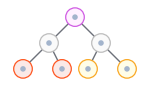

```mathematica
{d,δm}=FichetUltrametric[δL];
extree=BinaryTreeFromUltrametric[δm,"LeafLabels"->{"A","B","C","E"}];
{A,B}=PhyloTreeCone[δL,d];
special=FindSpecialVertex[δm,A,B];
weight=PropertyValue[{extree,special},VertexLabels];
gextree=PrettyTreeForm[extree,
ImageSize->150,FontSize->8,VertexSize->0.16,
VertexColors->{{1,2}->redScheme,{3,4}->orangeScheme,special->purpleScheme,{5,6}->whiteScheme}
]
Export[NotebookDirectory[]<>"prop1-3-max_L.pdf",gextree];
Export[NotebookDirectory[]<>"prop1-3-max_L_hg.pdf",TreeToHypergraph[extree,A,B,ImageSize->150,FontSize->7,VertexSize->0.65,"LeafLabels"->{"A","B","C","E"}]];
```

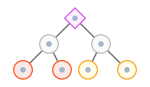
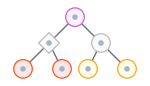
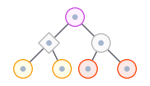

```mathematica
ext=ComputeExtreme[A,B];
ultrametrics=UltrametricFromVector/@ext[[All,2;;]];
extrees=BinaryTreeFromUltrametric[#,"LeafLabels"->{"A","B","C","E"}]&/@ultrametrics;
specials=Flatten[Position[#,weight]]&/@((Values@KeySort@PropertyValue[#,VertexLabels])&/@extrees);
maxsccNode={7,6,6};
gextrees=MapThread[PrettyTreeForm[#1,ImageSize->150,FontSize->8,VertexSize->0.16,
VertexColors->{{1,2}->redScheme,{3,4}->orangeScheme,special->purpleScheme,{5,6}->whiteScheme},"HighlightVertices"->#3
]&,{extrees,specials,maxsccNode}]
Table[Export[NotebookDirectory[]<>"prop1-3-ext_L"<>ToString[i]<>".pdf",gextrees[[i]]],{i,1,Length[gextrees]}];
Table[Export[NotebookDirectory[]<>"prop1-3-ext_L_hg"<>ToString[i]<>".pdf",TreeToHypergraph[extrees[[i]],A,B,ImageSize->150,FontSize->7,VertexSize->0.65,"LeafLabels"->{"A","B","C","E"}]],{i,1,Length[gextrees]}];
```

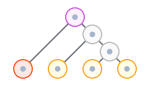

```mathematica
{d,δm}=FichetUltrametric[δR];
extree=BinaryTreeFromUltrametric[δm,"LeafLabels"->{"A","C","D","E"}];
{A,B}=PhyloTreeCone[δR,d];
special=FindSpecialVertex[δm,A,B];
weight=PropertyValue[{extree,special},VertexLabels];
gextree=PrettyTreeForm[extree,
ImageSize->150,FontSize->8,VertexSize->0.16,
VertexColors->{{1}->redScheme,{2,3,4}->orangeScheme,special->purpleScheme,{5,6}->whiteScheme}
]
Export[NotebookDirectory[]<>"prop1-3-max_R.pdf",gextree];
Export[NotebookDirectory[]<>"prop1-3-max_R_hg.pdf",TreeToHypergraph[extree,A,B,ImageSize->150,FontSize->7,VertexSize->0.65,"LeafLabels"->{"A","C","D","E"}]];
```

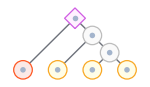
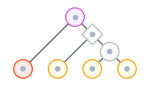
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ext=ComputeExtreme[A,B];
ultrametrics=UltrametricFromVector/@ext[[All,2;;]];
extrees=BinaryTreeFromUltrametric[#,"LeafLabels"->{"A","C","D","E"}]&/@ultrametrics;
specials=Flatten[Position[#,weight]]&/@((Values@KeySort@PropertyValue[#,VertexLabels])&/@extrees);
maxsccNode={7,7,6,6,6};
gextrees=MapThread[PrettyTreeForm[#1,ImageSize->150,FontSize->8,VertexSize->0.16,
VertexColors->{{1}->redScheme,{2,3,4}->orangeScheme,special->purpleScheme,{5,6}->whiteScheme},"HighlightVertices"->#3
]&,{extrees,specials,maxsccNode}]
Table[Export[NotebookDirectory[]<>"prop1-3-ext_R"<>ToString[i]<>".pdf",gextrees[[i]]],{i,1,Length[gextrees]}];
Table[Export[NotebookDirectory[]<>"prop1-3-ext_R_hg"<>ToString[i]<>".pdf",TreeToHypergraph[extrees[[i]],A,B,ImageSize->150,FontSize->7,VertexSize->0.65,"LeafLabels"->{"A","C","D","E"}]],{i,1,Length[gextrees]}];
```